# Euclidean Vector Introduction

A vector is a quantity that has both a magnitude and direction.

## Vector Basics

Let’s start by making a vector in the 2-D Cartesian plane.

Draw the vector v starting at point (0,0) and ending at point (1,1).

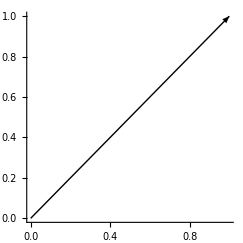

```mathematica
Graphics[{Arrow[{{0,0},{1,1}}]}, Axes -> True]
```

This vector describes a quantity that is pointed in the northeast direction. Its norm, or magnitude, is defined as √((x_2-x_1)^2+(y_2-y_1)^2).

Calculate the norm of v, or Norm[v].

```mathematica
Sqrt[(1-0)^2+(1-0)^2]
```

√2

Thus the magnitude of this vector v (||v||) can be said to be √2. This vector v would be written as {1,1} because it moves over 1 unit in the x direction and up 1 unit in the y direction.

## Unit Vectors

Unit vectors are vectors that have a direction but have a magnitude of 1.

Show the unit vector i in blue and j in red.

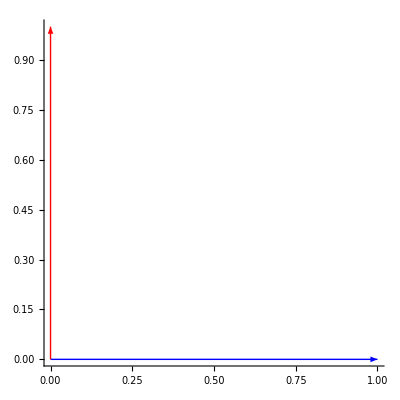

```mathematica
Graphics[{Blue,Thick,Arrow[{{0,0},{1,0}}],Red,Arrow[{{0,0},{0,1}}]},Axes->True]
```

The vector {1,1} could also be written as i + j where both terms have a coefficient of 1. Unit vector i corresponds to the x-component (horizontal) while j corresponds to the y-component (vertical).

## Vector Decomposition

In order to begin vector operations, we need to know how to get its components.

Find the vertical component of the vector {1,1}.

```mathematica
Norm[{1,1}]*Sin[Pi/4]
```

1

Using simple trigonometry by viewing the vector as a triangle’s hypotenuse, we can obtain the vertical component.

Display the vertical component graphically.

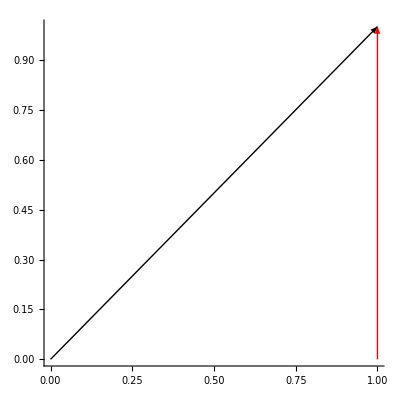

```mathematica
Graphics[{Arrow[{{0,0},{1,1}}],Red,Arrow[{{1,0},{1,1}}]},Axes -> True]
```

The horizontal component is very similar.

```mathematica
Norm[{1,1}]*Cos[Pi/4]
```

1

Display the horizontal component graphically.

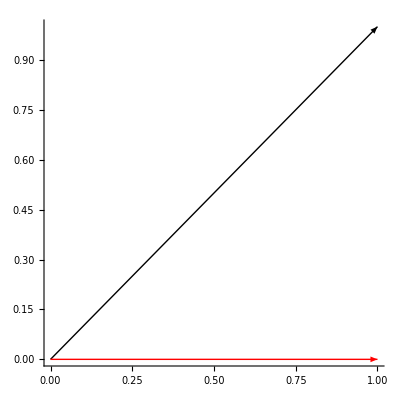

```mathematica
Graphics[{Arrow[{{0,0},{1,1}}],Red,Thick,Arrow[{{0,0},{1,0}}]},Axes->True]
```

Create your own vector and look at its components.

```mathematica
Manipulate[
Graphics[{
Arrow[{{0,0},{a,b}}],
Red,Thick,Arrow[{{0,0},{a,0}}],
Blue,Arrow[{{a,0},{a,b}}]},
PlotRange->{{-10,10},{-10,10}},Axes->True,
Epilog->{
Text[Style[a,Red,FontSize->20],{5,5}],
Text[Style[b,Blue,FontSize->20],{5,6}],
Text[Style[Norm[{a,b}],Black,FontSize->20],{5,7}]}],
{a,-10,10,0.1},{b,-10,10,0.1}]
```

## Vector Addition and Subtraction

Just like scalars, which have only a magnitude and no direction, vectors can undergo operations such as addition and subtraction.

Add the two vectors {3,2} and {0,4} together.

```mathematica
{3,2} + {0,4}
```

{3,6}

In a vector addition, individual components are added. We get {3,6} from {3+0, 2+4}. Subtraction works the same way.

Subtract the vector {5,2} from the vector {1,3}.

```mathematica
{1,3} - {5,2}
```

{-4,1}

## Vector Multiplication: Dot Product

Multiplication of vectors is a bit more complex. We’ll start with the dot product. The result of a dot product is not a vector but instead is a scalar with just a magnitude and no direction. What it shows is the projection of vector one along vector two.

Take the dot product of the vectors {4,1} and {2,1}.

```mathematica
{1,1}.{2,0}
```

2

It is obtained from 1*2 + 1*0.

Without knowing the components of a vector, the dot product can be obtained by:

```mathematica
Norm[{1,1}]*Norm[{2,0}]*Cos[Pi/4]
```

2

This is ||v||*||u||*cos(θ) where v and u are vectors and θ is the angle between them.

Let’s look at it graphically:

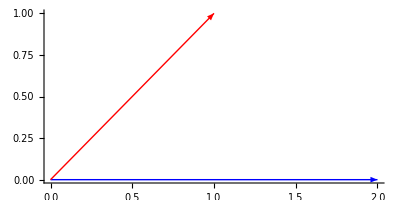

```mathematica
Graphics[{Blue,Thick,Arrow[{{0,0},{2,0}}],Red,Arrow[{{0,0},{1,1}}]}, Axes -> True]
```

From this we can easily see that there is no projection of the first vector onto the second vector that is along the y-axis, which is why in our dot product 1*2 + 1*0, the second term results in a 0.

Like scalar multiplication, order does not matter for a dot product.

```mathematica
{1,3}.{4,2}
```

10

```mathematica
{4,2}.{1,3}
```

10

## Vectors in 3-D

Just as vectors can exist in two dimensions, so they can exist in three dimensions.

Draw the vector {1,1,1}.

```mathematica
Graphics3D[Arrow[{{0,0,0},{1,1,1}}], Axes -> True]
```

-Graphics3D-

For ease, direction is described in spherical coordinates, and magnitude changes to √((x_2-x_1)^2+(y_2-y_1)^2+(z_2+z_1)^2).

Find the norm of the vector v = {1,2,3}.

```mathematica
Norm[{1,2,3}]
```

√14

In three dimensions, addition and taking the dot product work the exact same way but with an added term. Additionally, the unit vector in the third dimension is k.

Make your own 3-D vector.

```mathematica
Manipulate[Graphics3D[{
Text[Style[Norm[{a,b,c}],FontSize->20],{5,3,5}],
Blue,Arrow[{{0,0,0},{a,0,0}}],Text[Style[a,FontSize->20],{5,3,2}],
Red,Arrow[{{a,0,0},{a,b,0}}],Text[Style[b,FontSize->20],{5,3,3}],
Green,Arrow[{{a,b,0},{a,b,c}}],Text[Style[c,FontSize->20],{5,3,4}],
Black,Arrow[{{0,0,0},{a,b,c}}]},Axes -> True,
PlotRange->{{0,10},{0,10},{0,10}}],
{a,0,10},{b,0,10},{c,0,10}]
```

## Vector Multiplication: Cross Product

The cross product takes two vectors and results in a vector that is orthogonal to both.

```mathematica
Cross[{1,0,0},{0,1,0}]
```

{0,0,1}

This time the output is a vector and not a scalar like the dot product.

The magnitude of the cross product is the same as ||v||*||u||*sin(θ) where θ is the angle between the two vectors.

```mathematica
Norm[{1,0,0}]*Norm[{0,1,0}]*Sin[Pi/2]
```

1

This is the same as

```mathematica
Norm[{0,0,1}]
```

1

Let’s see what these three vectors look like.

```mathematica
Graphics3D[{Blue,Arrow[{{0,0,0},{1,0,0}}],Red,Arrow[{{0,0,0},{0,1,0}}],Green,Arrow[{{0,0,0},{0,0,1}}]},Axes -> True]
```

-Graphics3D-

The cross product is the same as finding the determinant of the matrix

```mathematica
MatrixForm[{{i,j,k},{1,0,0},{0,1,0}}]
```

(i | j | k
1 | 0 | 0
0 | 1 | 0)

```mathematica
Det[{{i,j,k},{1,0,0},{0,1,0}}]
```

k

where i, j, and k are the x, y, and z unit vectors respectively. The result of the cross product of vector {1,0,0} and {0,1,0} is {0,0,1}, or k.

Unlike the dot product, the order of vectors in a cross product does matter.

```mathematica
Cross[{1,0,0},{0,1,0}]
```

{0,0,1}

```mathematica
Cross[{0,1,0},{1,0,0}]
```

{0,0,-1}

While order matters, the result of changing the order will be the same vector multiplied by -1.

```mathematica
Cross[{a,b,c},{x,y,z}]
```

{-c y+b z,c x-a z,-b x+a y}

Now let’s do flip the order and multiply by -1.

```mathematica
Cross[{x,y,z},{a,b,c}]
```

{c y-b z,-c x+a z,b x-a y}

```mathematica
-1 * Cross[{x,y,z},{a,b,c}]
```

{-c y+b z,c x-a z,-b x+a y}

We can see the results are the same. That’s all there is to know about basic Euclidean vectors!

Further Explorations

Parametric Equations of Vectors

Vector Fields

Tangent Vectors

Authorship information

Ethan Truelove

19 June 2017

ethan.truelove@me.com